## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/reduction/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.417552 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.1.0 for Mac OS X x86

date: May 12, 2020, time: 02:01:12

nb: /Users/dantopa/Mathematica_files/nb/ert/rcs/reduction/alias-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.417552 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## data

### import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
σ=RotateLeft[meanRCS,180];
{m,n}=Dimensions[σ]
```

{28,361}

## plot

```mathematica
θticks={{1,"-180°"},{91,"-90°"},{181,"0°"},{271,"90°"},{361,"180°"}};
```

```mathematica
fticks={{Automatic,Automatic},{θticks,Automatic}};
```

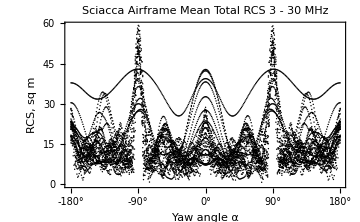

```mathematica
gnew=ListPlot[σ,
isize,
Frame->True,
FrameTicks->fticks,
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->"Sciacca Airframe"<>lf<>"Mean Total RCS 3 - 30 MHz",
Joined->False,
PlotStyle->Black]
```

```mathematica
tresExport["rcs-all-frequencies",gnew]
```

### plot utility

```mathematica
Clear[myPlot];
myPlot[ψ_,str_String,options___]:=Module[{g},
g=ArrayPlot[Reverse[ψ],
options,
ColorFunction->(Hue[(1-Rescale[# ,{mn,mx}])magicnumber]&),
ColorFunctionScaling->False,
FrameTicks->{{{1,3},{8,10},{18,20},{28,30}},θticks,{{1,100},{4,50},{8,30},{13,20},{18,15},{28,10}},None},
FrameLabel->{"Frequency ν, MHZ","Yaw α","Wavelength λ, m",None},
PlotLabel->title<>lf<>str,
AspectRatio->1/GoldenRatio,
PlotLegends->Placed[Automatic,After]]]
myPlot[meanRCS,"Mean Total RCS, sq m",isize]
```

StringJoin::string: String expected at position 1 in title<>
Mean Total RCS, sq m.

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

```mathematica
361 28
```

10108

```mathematica
Product[Dimensions[σ][[k]],{k,2}]
```

10108

```mathematica
{m,n}=Dimensions[σ]
```

{28,361}

## experiment

### plot utility

```mathematica
νticks={{1,3},{8,10},{18,20},{28,30}};
λticks={{1,100},{15,20},{4,50},{28,10}};
θticks={{1,"-180°"},{91,"-90°"},{181,"0°"},{271,"90°"},{361,"180°"}};
```

```mathematica
Clear[myArrayPlot];
myArrayPlot[ψ_,str_String,options___]:=Module[{g},
g=ArrayPlot[ψ,
options,
PlotLabel->str,
ColorFunction->(Hue[(1-Rescale[#,{mn,mx}])magicnumber]&),
ColorFunctionScaling->False,
FrameTicks->{{νticks,λticks},{θticks,None}},
FrameLabel->{"Frequency, MHz","Azimuth","Wavelength, m",None},
PlotLegends->Placed[Automatic,After],
ImageSize->6 72,
AspectRatio->1/GoldenRatio];
Return[g];
]
```

```mathematica
title="Sciacca airframe Mean Total RCS, sq m";
g000=myArrayPlot[meanRCS,title]
```

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

```mathematica
361 28
```

10108

```mathematica
Product[Dimensions[σ][[k]],{k,2}]
```

10108

```mathematica
{m,n}=Dimensions[σ]
```

{28,361}

## 2 sample

```mathematica
prime=2;
```

```mathematica
new=Table[
meanRCS[[μ,ν]]
,{μ,m},{ν,1,n-1,prime}];
Dimensions[new]
```

{28,180}

```mathematica
θticks={{1,"-180°"},{91/prime,"-90°"},{181/prime,"0°"},{271/prime,"90°"},{361/prime,"180°"}};
```

```mathematica
title:="Sciacca airframe Mean Total RCS, sq m"<>lf<>"Sample every "<>ToString[prime]<>" terms";
g000=myArrayPlot[new,title]
```

```mathematica
multiExport["reduce-"<>pad[prime],g000]
```

## 3 sample

```mathematica
prime=3;
```

```mathematica
new=Table[
meanRCS[[μ,ν]]
,{μ,m},{ν,1,n-1,prime}];
Dimensions[new]
```

{28,120}

```mathematica
θticks={{1,"-180°"},{91/prime,"-90°"},{181/prime,"0°"},{271/prime,"90°"},{361/prime,"180°"}};
```

```mathematica
title:="Sciacca airframe Mean Total RCS, sq m"<>lf<>"Sample every "<>ToString[prime]<>" terms";
g000=myArrayPlot[new,title]
```

```mathematica
multiExport["reduce-"<>pad[prime],g000]
```

## 6 sample

```mathematica
prime=6;
```

```mathematica
new=Table[
meanRCS[[μ,ν]]
,{μ,m},{ν,1,n-1,prime}];
Dimensions[new]
```

{28,60}

```mathematica
θticks={{1,"-180°"},{91/prime,"-90°"},{181/prime,"0°"},{271/prime,"90°"},{361/prime,"180°"}};
```

```mathematica
title:="Sciacca airframe Mean Total RCS, sq m"<>lf<>"Sample every "<>ToString[prime]<>" terms";
g000=myArrayPlot[new,title]
```

```mathematica
multiExport["reduce-"<>pad[prime],g000]
```

## 12 sample

```mathematica
prime=12;
```

```mathematica
new=Table[
meanRCS[[μ,ν]]
,{μ,m},{ν,1,n-1,prime}];
Dimensions[new]
```

{28,30}

```mathematica
θticks={{1,"-180°"},{91/prime,"-90°"},{181/prime,"0°"},{271/prime,"90°"},{361/prime,"180°"}};
```

```mathematica
title:="Sciacca airframe Mean Total RCS, sq m"<>lf<>"Sample every "<>ToString[prime]<>" terms";
g000=myArrayPlot[new,title]
```

```mathematica
multiExport["reduce-"<>pad[prime],g000]
```

## 20 sample

```mathematica
prime=20;
```

```mathematica
new=Table[
meanRCS[[μ,ν]]
,{μ,m},{ν,1,n-1,prime}];
Dimensions[new]
```

{28,18}

```mathematica
θticks={{1,"-180°"},{91/prime,"-90°"},{181/prime,"0°"},{271/prime,"90°"},{361/prime,"180°"}};
```

```mathematica
title:="Sciacca airframe Mean Total RCS, sq m"<>lf<>"Sample every "<>ToString[prime]<>" terms";
g000=myArrayPlot[new,title]
```

```mathematica
multiExport["reduce-"<>pad[prime],g000]
```

## weaponize

### update plot routine

```mathematica
Clear[myNakedPlot];
myNakedPlot[ψ_,options___]:=Module[{g},
g=ArrayPlot[Reverse[ψ],
options,
ColorFunction->(Hue[(1-Rescale[#,{mn,mx}])magicnumber]&),
ColorFunctionScaling->False,
FrameTicks->{{{1,3},{8,10},{18,20},{28,30}},θticks,{{1,100},{4,50},{8,30},{13,20},{18,15},{28,10}},None},
FrameLabel->{"Frequency ν, MHZ","Yaw α","Wavelength λ, m",None},
PlotLabel->title,
AspectRatio->1/GoldenRatio]
(* PlotLegends->Placed[Automatic,After]]*) ]
```

### loop

```mathematica
Prime[10]
```

29

```mathematica
list={2,3,4,5,6,8,9,10,12,15,18,20};
```

```mathematica
Do[
(* average *)
new=Table[
tbl=Table[meanRCS[[μ,ν+k]],{k,0,prime-1}];
Mean[tbl]
,{μ,m},{ν,1,n-1,prime}];
Print["factor = ",prime];
Print["dimensions of reduced array = ",Dimensions[new]];
(* new ticks *)
λ=Last[Dimensions[new]];
θticks={{1,"-180°"},{λ/4,"-90°"},{λ/2,"0°"},{(3λ)/4,"90°"},{λ,"180°"}};
(* θticks={{1,"-180°"},{Round[λ/4],"-90°"},{Round[λ/2],"0°"},{Round[(3λ)/4],"90°"},{Round[λ],"180°"}}; *)
(* adjust title *)
title="Average "<>ToString[prime]<>" values";
(* render *)
gnew=myNakedPlot[new,isize];
(* output *)
Export[dirGraph<>"sampling-"<>pad[prime]<>".pdf",gnew];
,{prime,list}]
```

factor = 2

dimensions of reduced array = {28,180}

factor = 3

dimensions of reduced array = {28,120}

factor = 4

dimensions of reduced array = {28,90}

factor = 5

dimensions of reduced array = {28,72}

factor = 6

dimensions of reduced array = {28,60}

factor = 8

dimensions of reduced array = {28,45}

factor = 9

dimensions of reduced array = {28,40}

factor = 10

dimensions of reduced array = {28,36}

factor = 12

dimensions of reduced array = {28,30}

factor = 15

dimensions of reduced array = {28,24}

factor = 18

dimensions of reduced array = {28,20}

factor = 20

dimensions of reduced array = {28,18}

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```